```mathematica
ASSIGNMENT - 3
```

```mathematica
Om Gupta
214047
```

```mathematica
eqn1a=D[y[x],{x,3}]-5 D[y[x],{x,2}]+8 D[y[x],x]-4 y[x]==0;
sol1a=DSolve[eqn1a,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(2 x) x C[3]}}

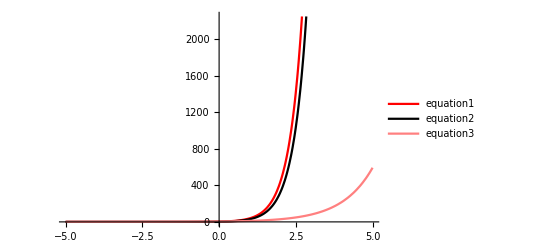

```mathematica
Plot[{pa1, pa2, pa3}, {x, -5, 5}, PlotStyle -> {Red, Black, Pink},
PlotLegends -> {"equation1", "equation2", "equation3"}]
```

```mathematica
eqn1b = D[y[x], {x, 3}] + 3 D[y[x], {x, 2}] - 25 D[y[x], x] + 21 y[x] == 0;
sol1b = DSolve[eqn1b, y[x], x]
```

{{y[x]→ⅇ^(-7 x) C[1]+ⅇ^x C[2]+ⅇ^(3 x) C[3]}}

```mathematica
pb1 = y[x] /. sol1b /. {C[1] -> 1, C[2] -> 2, C[3] -> 3};
pb2 = y[x] /. sol1b /. {C[1] -> 2, C[2] -> 3, C[3] -> 9};
pb3 = y[x] /. sol1b /. {C[1] -> 7, C[2] -> 4, C[3] -> 7}
```

{7 ⅇ^(-7 x)+4 ⅇ^x+7 ⅇ^(3 x)}

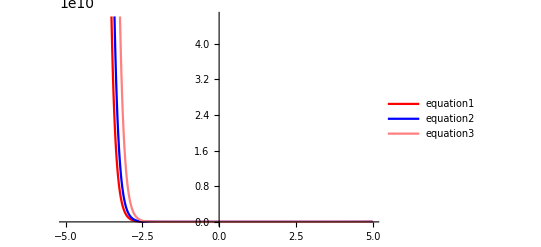

```mathematica
Plot[{pb1, pb2, pb3}, {x, -5, 5}, PlotStyle -> {Red, Blue, Pink},
PlotLegends -> {"equation1", "equation2", "equation3"}]
```